## Prepare

```mathematica
imgsize=700;
imgpadding={{70, 20}, {50, 10}};
```

## Solving Eqns

I use x̄=omega x as variable x here. In other words, the x I am going to use is in fact omega x.

```mathematica
ClearAll[sin2thetav,α0,α1,β,θ]
```

```mathematica
eqn1= I c1'[x]==Cos[2θ]/2(α0+α1 Cos[β x])c1[x]+Sin[2θ]/2(α0+α1 Cos[β x])c2[x]Exp[-I x]
eqn2=I c2'[x]==-Cos[2θ]/2(α0+α1 Cos[β x])c2[x]+ Sin[2θ]/2(α0+α1 Cos[β x])c1[x] Exp[I x]
```

ⅈ c1'[x]==1/2 c1[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(-ⅈ x) c2[x] (α0+α1 Cos[x β]) Sin[2 θ]

ⅈ c2'[x]==-1/2 c2[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(ⅈ x) c1[x] (α0+α1 Cos[x β]) Sin[2 θ]

Initial condition is given to be in instantaneous basis the light state is 1 while the heavy state is 0, transform to vacuum basis

```mathematica
{0.9999500729766898,-0.009992574939063952}
```

{0.99995,-0.00999257}

```mathematica
init1=c1[0]==0.9999500729766898
init2=c2[0]==-0.009992574939063952
```

c1[0]==0.99995

c2[0]==-0.00999257

```mathematica
solana=DSolve[{eqn1,eqn2,init1,init2},{c1,c2},x]
```

DSolve[{ⅈ c1'[x]==1/2 c1[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(-ⅈ x) c2[x] (α0+α1 Cos[x β]) Sin[2 θ],ⅈ c2'[x]==-1/2 c2[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(ⅈ x) c1[x] (α0+α1 Cos[x β]) Sin[2 θ],c1[0]==0.99995,c2[0]==-0.00999257},{c1,c2},x]

The parameters to be used

```mathematica
θv=0.573*Pi/180;
sin2thetav=Sin[2*θv]
cos2thetav=√(1-sin2thetav^2);
α0=Cos[2θv]/2;
α1=0.1α0;
β=2Pi/(5.27*300/(4*197))
θ=ArcSin[sin2thetav]/2;
omegav=7.5*10^(-11);(*eV, delta^2m= 3*10^(-3)eV^2, E =20MeV*)
```

0.0200001

3.13166

Kneller calculated x ∈ up to 10^10 cm, which corresponds to ω x=

```mathematica
0.75*10^(7)/197
```

38071.1

(* omega is not being used in this calculation but is needed in adiabatic reference *)

```mathematica
(*omega = 2*10^(-3)/(2*10)*)
```

```mathematica
endpoint=800
```

800

```mathematica
solnum=NDSolve[{eqn1,eqn2,init1,init2},{c1,c2},{x,0,endpoint}]
```

{{c1→InterpolatingFunction[{{0., 800.}}, <>],c2→InterpolatingFunction[{{0., 800.}}, <>]}}

```mathematica
solnum[[1]]
```

{c1→InterpolatingFunction[{{0., 800.}}, <>],c2→InterpolatingFunction[{{0., 800.}}, <>]}

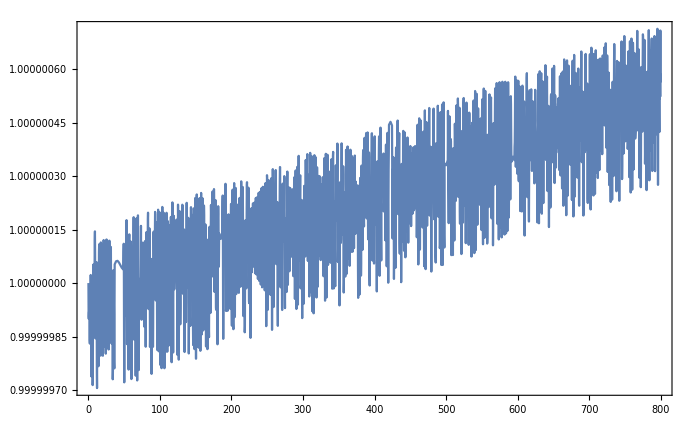

```mathematica
normnum=Plot[Evaluate[Abs[c1[x]]^2+Abs[c2[x]]^2/.solnum[[1]]],{x,0,endpoint},PlotRange->All,ImageSize->imgsize,Frame->True]
```

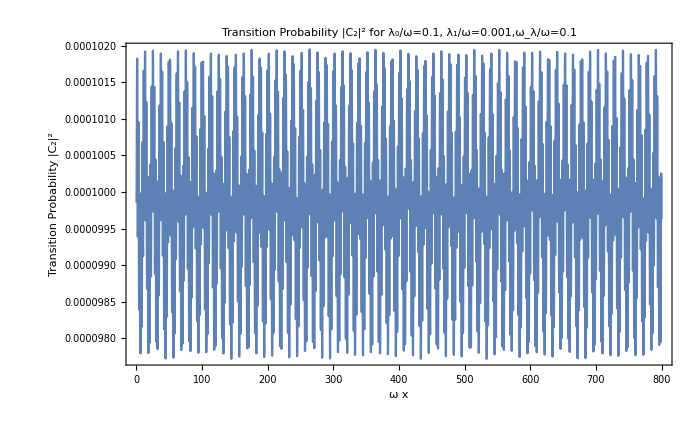

```mathematica
numP=Plot[Evaluate[Abs[c2[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solnum[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_2|^2"},ImagePadding->imgpadding]
```

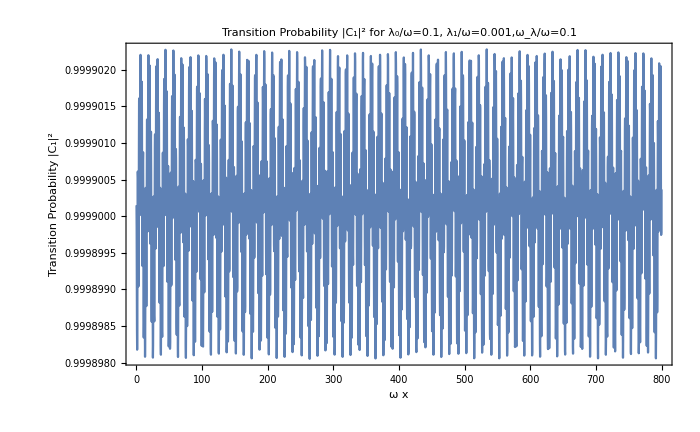

```mathematica
numP1=Plot[Evaluate[Abs[c1[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.solnum[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_1|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_1|^2"},ImagePadding->imgpadding]
```

### From Vacuum Mass Eigenstates to Flavor Eigenstates

```mathematica
mat={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
```

Flavor basis wavefunction is

```mathematica
c1Fun=c1/.solnum[[1]]
c2Fun=c2/.solnum[[1]]
{ce[x_],cx[x_]}=mat.{c1Fun[x],c2Fun[x]}
```

InterpolatingFunction[{{0., 800.}}, <>]

InterpolatingFunction[{{0., 800.}}, <>]

{0.0100006 InterpolatingFunction[{{0., 800.}}, <>][x]+0.99995 InterpolatingFunction[{{0., 800.}}, <>][x],0.99995 InterpolatingFunction[{{0., 800.}}, <>][x]-0.0100006 InterpolatingFunction[{{0., 800.}}, <>][x]}

Initial electron flavor probability is

```mathematica
initialEFlavorProb=NumberForm[Abs[ce[0]]^2/(Abs[ce[0]]^2+Abs[cx[0]]^2),2]
```

1.

```mathematica
normFnum=Plot[Evaluate[Abs[ce[x]]^2+Abs[cx[x]]^2],{x,0,endpoint},PlotRange->All,ImageSize->imgsize,Frame->True]
```

-Graphics-

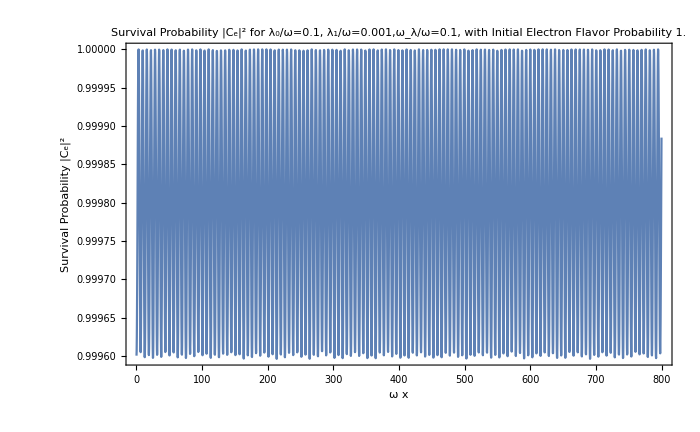

```mathematica
numPF=Plot[Evaluate[Abs[ce[x]]^2/(Abs[ce[x]]^2+Abs[cx[x]]^2)],{x,0,endpoint},PlotRange->All,PlotLabel->"Survival Probability |C_e|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1, with Initial Electron Flavor Probability "<>ToString[initialEFlavorProb],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Survival Probability |C_e|^2"},ImagePadding->imgpadding]
```

## Adiabatic Limit

Just as an comparison

```mathematica
temp = {{Cos[t-tx],Sin[t-tx]},{-Sin[t-tx],Cos[t-tx]}}
```

{{Cos[t-tx],Sin[t-tx]},{-Sin[t-tx],Cos[t-tx]}}

```mathematica
Inverse[temp].temp//FullSimplify
```

{{1,0},{0,1}}

```mathematica
Inverse[temp]//FullSimplify//MatrixForm
```

(Cos[t-tx] | -Sin[t-tx]
Sin[t-tx] | Cos[t-tx])

Calculate the angles

```mathematica
sin2thetax[x_]=sin2thetav/(√(1+(α0+α1*Cos[β x])^2-2(α0+α1*Cos[β x])cos2thetav))
```

0.0200001/(√(1-1.9996 (0.4999+0.04999 Cos[3.13166 x])+(0.4999+0.04999 Cos[3.13166 x])^2))

```mathematica
thetax[x_]=ArcSin[sin2thetax[x]]/2;
thevac=ArcSin[sin2thetav]/2;
```

```mathematica
thetax[0]
```

0.0222122

energy difference

```mathematica
deltaE[x_]=(√((α0+α1*Cos[β x])^2+1-2(α0+α1*Cos[β x])cos2thetav))/2;
```

probability of the first vacuum eigenstate is

```mathematica
adProbVac1[x_]=Abs[(Cos[thevac-thetax[x]])Cos[thevac-thetax[0]]]^2+Abs[Sin[thevac-thetax[x]] Sin[thevac-thetax[0]] ]^2+Cos[thevac-thetax[x]]Cos[thevac-thetax[0]]Sin[thevac-thetax[x]]Sin[thevac-thetax[0]]2Cos[deltaE[x]x]
```

0.999851 Abs[Cos[0.0100007-1/2 ArcSin[0.0200001/(√(1-1.9996 (0.4999+0.04999 Cos[3.13166 x])+(0.4999+0.04999 Cos[3.13166 x])^2))]]]^2+0.000149112 Abs[Sin[0.0100007-1/2 ArcSin[0.0200001/(√(1-1.9996 (0.4999+0.04999 Cos[3.13166 x])+(0.4999+0.04999 Cos[3.13166 x])^2))]]]^2-0.0244205 Cos[0.0100007-1/2 ArcSin[0.0200001/(√(1-1.9996 (0.4999+0.04999 Cos[3.13166 x])+(0.4999+0.04999 Cos[3.13166 x])^2))]] Cos[1/2 x √(1-1.9996 (0.4999+0.04999 Cos[3.13166 x])+(0.4999+0.04999 Cos[3.13166 x])^2)] Sin[0.0100007-1/2 ArcSin[0.0200001/(√(1-1.9996 (0.4999+0.04999 Cos[3.13166 x])+(0.4999+0.04999 Cos[3.13166 x])^2))]]

```mathematica
adProbVac1[2]
```

0.99997

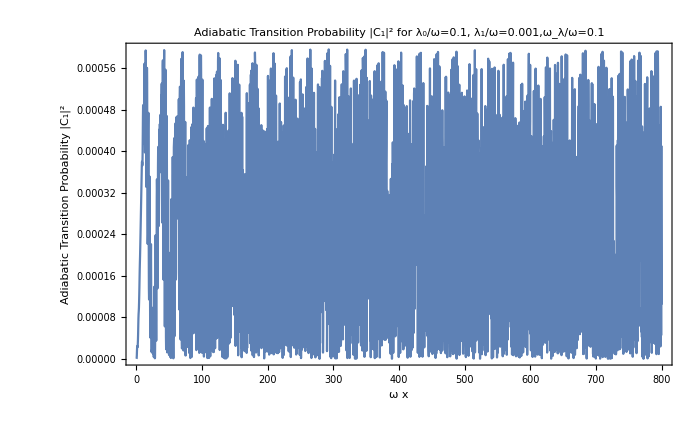

```mathematica
Plot[1-adProbVac1[x],{x,0,endpoint},PlotRange->All,PlotLabel->"Adiabatic Transition Probability |C_1|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Adiabatic Transition Probability |C_1|^2"},ImagePadding->imgpadding]
```

### From Vacuum Eigenbasis to Instantaneous Eigenbasis

The instantaneous eigenbasis set by constant matter is

```mathematica
sin2thetaxConst=sin2thetav/(√(1+(α0)^2-2(α0)cos2thetav))
```

0.0399763

```mathematica
thetaxConst=ArcSin[sin2thetaxConst]/2;
```

Rotation matrix from vacuum basis to inst basis is

```mathematica
vac2instRot = {{Cos[thevac-thetaxConst],Sin[thevac-thetaxConst]},{-Sin[thevac-thetaxConst],Cos[thevac-thetaxConst]}}
```

{{0.99995,-0.00999257},{0.00999257,0.99995}}

The amplitude of heavy state is given by

```mathematica
instWaveFunc[x_]=vac2instRot.{c1[x],c2[x]}/.solnum[[1]]
```

{-0.00999257 InterpolatingFunction[{{0., 800.}}, <>][x]+0.99995 InterpolatingFunction[{{0., 800.}}, <>][x],0.99995 InterpolatingFunction[{{0., 800.}}, <>][x]+0.00999257 InterpolatingFunction[{{0., 800.}}, <>][x]}

```mathematica
instWaveFunc[1][[1]]
```

0.968906-0.247242 ⅈ

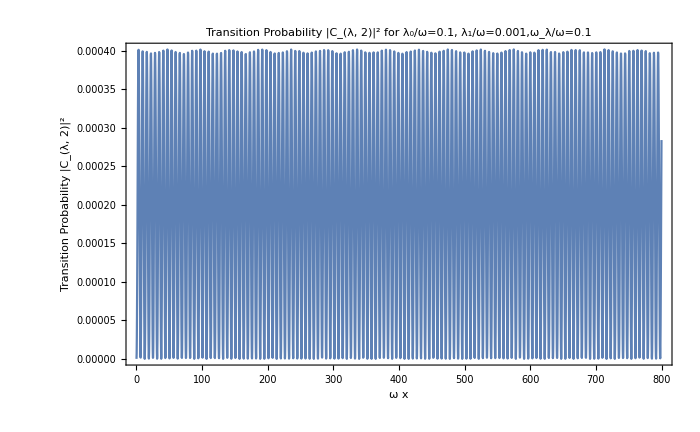

```mathematica
numPInstHeavy=Plot[Evaluate[Abs[instWaveFunc[x][[2]]]^2/.solnum[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

```mathematica
Transpose[vac2instRot].{1,0}
```

{0.99995,-0.00999257}

## Approximation: very small perturbation

```mathematica
eqnc2pert=c2pert''[x]+(α1/α0 Sin[β x]-I)c2pert'[x]+(1/2 α0(1-cos2thetav)(1+α1/α0 Cos[β x])-1/4 α0)c2pert[x]==0
```

c2pert[x] (-0.124975+0.0000499957 (1+0.1 Cos[3.13166 x]))+(-ⅈ+0.1 Sin[3.13166 x]) c2pert'[x]+c2pert''[x]==0

```mathematica
solc2pert=NDSolve[{eqnc2pert,c2pert[0]==0,c2pert'[0]==-I sin2thetav/2 α0},c2pert,{x,0,800}]
```

{{c2pert→InterpolatingFunction[{{0., 800.}}, <>]}}

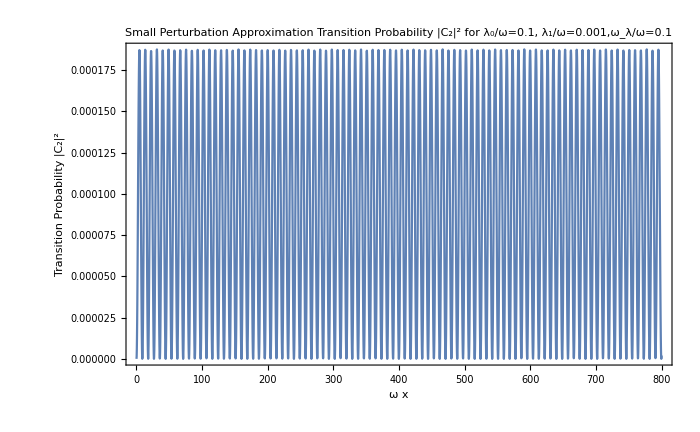

```mathematica
numP=Plot[Evaluate[Abs[c2pert[x]]^2/.solc2pert[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Small Perturbation Approximation Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_2|^2"},ImagePadding->imgpadding]
```

## TEMP

```mathematica
DSolve[eta[x]+x D[eta[x],x]==lambda[x] Cos[2theta]/2,eta,x]
```

{{eta→Function[{x},C[1]/x+(∫_1^x 1/2 Cos[2 theta] lambda[K[1]]ⅆK[1])/x]}}